```mathematica
(* Import RHP library and set directory for files *)
AppendTo[$Path, " Your path to the RHPackage-master package here "];
<<RiemannHilbert`;
```

```mathematica
λ={ -0.5+1.0I, 0.5+1.0I};n=Length[λ]-1;
λstart=λ*;
Print["Initial λ"]
λend=λ
w[z_]:=Product[√((z-λstart[[i]])/(z-λend[[i]]))(z-λend[[i]]), {i,n+1}];
K1[ k_]:= N[NIntegrate[(I(Re[λstart[[1]]]+I x)^(k-1))/w[(Re[λstart[[1]]]+I x-10^-10)],{x,Im[ λstart[[1]]], Im[λend[[1]]]}]];

K2[ k_]:= N[NIntegrate[(I(Re[λstart[[2]]]+I x)^(k-1))/w[(Re[λstart[[2]]]+I x-10^-10)],{x,Im[ λstart[[2]]], Im[λend[[2]]]}]];
K[k_, j_]:=Switch[j, 1, K1[k], 2, K2[k]];
If [n>1,Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-1], {-2Pi I}]]],Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-2Pi I}]]] ;
W0[ξ_]=SeriesCoefficient[Simplify[Series[w[z]/(ξ-z), {z, Infinity, 1}]], 0];
(* Compiting matrix new \lambda so that we have periodicity *)

f00=1/(2π I)Cf[[1]] N[NIntegrate[(I W0[Re[λstart[[1]]]+I x])/w[(Re[λstart[[1]]]+I x-10^-10)],{x, Im[λstart[[1]]], Im[λend[[1]]]}]]+
1/(2π I)Cf[[2]] N[NIntegrate[(I W0[Re[λstart[[2]]]+I x])/w[(Re[λstart[[2]]]+I x-10^-10)],{x,Im[ λstart[[2]]], Im[λend[[2]]]}]];
Print["New λ"]
λstart=λstart+Re[f00]
λend=λend+Re[f00];
(* Compiting new matrix K and w and Cf *)
w[z_]:=Product[√((z-λstart[[i]])/(z-λend[[i]]))(z-λend[[i]]), {i,1, n+1}];
K1[ k_]:= N[NIntegrate[(I(Re[λstart[[1]]]+I x)^(k-1))/w[(Re[λstart[[1]]]+I x-10^-10)],{x,Im[ λstart[[1]]], Im[λend[[1]]]}]];
K2[ k_]:= N[NIntegrate[(I(Re[λstart[[2]]]+I x)^(k-1))/w[(Re[λstart[[2]]]+I x-10^-10)],{x,Im[ λstart[[2]]], Im[λend[[2]]]}]];
K[k_, j_]:=Switch[j, 1, K1[k], 2, K2[k]];
If [n>1,Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-1], {-2Pi I}]]],Cf=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-2Pi I}]]] ;
Switch[n,
2,
Cg=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]],  {-4Pi I , -2Pi I Total[ λstart+λend ]}]],
1,
Cg=Join[{0},{-2Pi I Total[ λstart+λend ]/K[ 1,2]}],
_,Cg=Join[{0},LinearSolve[Transpose[Table[K[k, j], {j, 2, n+1}, {k, 1, n}]], Join[ConstantArray[0, n-2], {-4Pi I, -2Pi I Total[ λstart+λend ]}]]]
];
W0[ξ_]=SeriesCoefficient[Simplify[Series[w[z]/(ξ-z), {z, Infinity, 1}]], 0];
f0=1/(2π I)Cf[[1]] N[NIntegrate[(I W0[Re[λstart[[1]]]+I x])/w[(Re[λstart[[1]]]+I x-10^-10)],{x, Im[λstart[[1]]], Im[λend[[1]]]}]]+
1/(2π I)Cf[[2]] N[NIntegrate[(I W0[Re[λstart[[2]]]+I x])/w[(Re[λstart[[2]]]+I x-10^-10)],{x,Im[ λstart[[2]]], Im[λend[[2]]]}]];
If[Abs[f0]>10^-3, Print["f_0 is too large"]]
```

Initial λ

{-0.5+1. ⅈ,0.5+1. ⅈ}

New λ

{0.278035-1. ⅈ,1.27803-1. ⅈ}

```mathematica
{0.27803487305674146-1. ⅈ,1.2780348730567415-1. ⅈ}
```

starting Phase

{0.4,0.8}

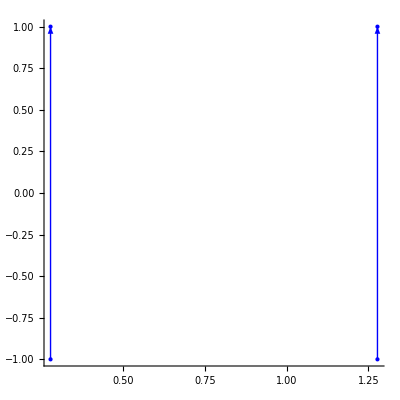

```mathematica
(* Introducing phase *)
nλ=40;nt=2^8;
Print["starting Phase"]
ϕin={0.4, 0.8}
Tnorm=Abs[2 π/Re[Cf[[2]]]];
(* Introducing jump matrix *)
Clear[G];
G[_][_,_?InfinityQ]:=IdentityMatrix[2];
G[_][_,_?ZeroQ]:=IdentityMatrix[2];
Do[G[i][x_,z_]=({{0z, I Exp[-I(Cf[[i]] x)]Exp[-I ϕin[[i]]]}, {I Exp[I(Cf[[i]]x)]Exp[I ϕin[[i]]], 0z}})/.Underflow[]->0, {i, 1, n+1}];
GG[p_,x_]:=
{
Fun[G[1][x,#]&,Line[{λstart[[1]],λend[[1]]}],p],

Fun[G[2][x,#]&,Line[{λstart[[2]],λend[[2]]}],p]
};
DomainPlot[GG[20,0.2], AspectRatio->1, PlotRange->All]
```

Period (L)

2.0189

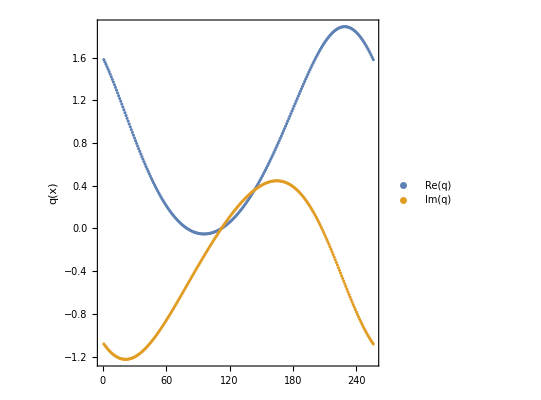

```mathematica
(* Solving RH problem to compute q *)
Print["Period (L)"]
Tnorm
trange=Range[-Tnorm/2, Tnorm/2, Tnorm/(nt-1)]+Tnorm/2;  (*nonsymmetrical!!!!*)
q=0 trange;
For[ix=1,ix<=Length[trange],ix++,
U=RHSolve[GG[nλ,trange[[ix]]]];
q[[ix]]=-1/π DomainIntegrate[U][[1,2]];
];
ListPlot[{Re[q], Im[q]}, Frame->True, FrameStyle->Directive[Medium, Bold], PlotStyle->Bold,FrameLabel->{None,"q(x)"}, PlotLegends->Placed[{"Re(q)", "Im(q)"}, Above], AspectRatio->1]
```

```mathematica
(* Computing \mu and a_1 , a_0 ; Solving Dirac system on the first step*)
qfun=Interpolation[Partition[Riffle[trange, q],2], InterpolationOrder->6];
MM[k_]:=N[NDSolveValue[{D[Φ[t],t]==Dot[({{-I k, qfun[t]}, {-Conjugate[qfun[t]], I k}}),Φ[t]], Φ[0]==IdentityMatrix[2]}, Φ[Tnorm], {t, 0, Tnorm}]];
```

```mathematica
U=RHSolve[GG[1000,0]];
q00=-1/π DomainIntegrate[U][[1,2]];
Print["q(00)"]
-1/π DomainIntegrate[U][[1,2]]
A1=Im[λend[[1]]];A2=Im[λend[[2]]];
B1=Re[λend[[1]]];B2=Re[λend[[2]]];
a1=-(B1+B2);
a0=1/2(-(B1+B2)^2+(Abs[λend[[2]]])^2+(Abs[λend[[1]]])^2+4B1*B2-(Abs[q00])^2);
mu1=(a1*a0+B1(Abs[λend[[2]]])^2+B2(Abs[λend[[1]]])^2)/(Abs[q00])^2;

mu2=Sqrt[Abs[((Abs[λend[[1]]])^2(Abs[λend[[2]]])^2-(a0)^2)/(Abs[q00])^2-mu1^2]];
Print["a1"]
a1
Print["a0"]
a0
Print["mu"]
mu1+I mu2
Print["M_12(mu_+)"]
MM[mu1+I mu2][[1,2]] (* Checking which one is zero of M_{12}*)
Print["M_12(mu_-)"]
MM[mu1-I mu2][[1,2]]
Print["(delta^2-4) (mu)"]
M[z_]:=(MM[z][[1,1]]+MM[z][[2,2]])^2-4;
M[mu1+I mu2] (* Checking that it is not zero of \delta^2-4*)
```

q(00)

1.58441-1.08395 ⅈ

a1

-1.55607

a0

-0.487319

mu

0.778035+0.316257 ⅈ

M_12(mu_+)

-0.000590439-0.000892097 ⅈ

M_12(mu_-)

0.575201+0.840734 ⅈ

(delta^2-4) (mu)

-4.00902-1.0395×10^-6 ⅈ

R(infty)

0.0000125137-0.0000667125 ⅈ

(F-sqrt(P))(mu)

0.+5.55112×10^-17 ⅈ

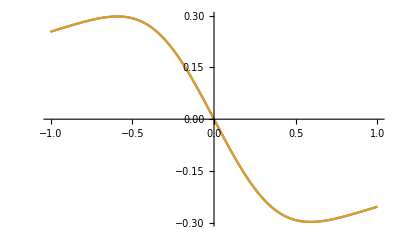

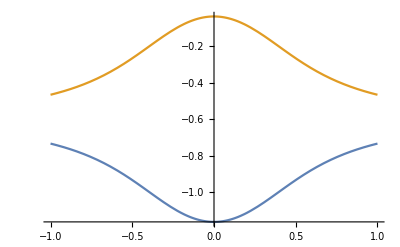

-Graphics-

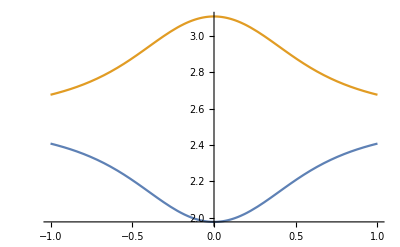

```mathematica
(* Introducing J00*)
F[z1_]:=z1^2+a1 z1+a0;
w[z_]:=Product[√((z-λstart[[i]])/(z-λend[[i]]))(z-λend[[i]]), {i,1, n+1}];
R[z2_]:=-I/(-Conjugate[q00](z2-(mu1-I mu2)))(F[z2]-w[z2]);

Print["R(infty)"]
R[10000-10000I] (* Checking branch*)
Print["(F-sqrt(P))(mu)"]
F[mu1-I mu2]-w[mu1-I mu2] (* Chacking if we need to multiply by fractional function*)
J002[z4_]:=-(ⅇ^(4π ⅈ Tnorm))^0(MM[z4][[1,2]])/(MM[z4][[2,1]]);
tilJ00[z5_]:=Sqrt[J002[z5]]
(*Plot[{Re[1/2 Log[J002[Re[λstart[[2]]]+10^-10+I y]]],Re[1/2 Log[J002[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]
Plot[{Im[1/2 Log[J002[Re[λstart[[2]]]+10^-10+I y]]],Im[1/2 Log[J002[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]*)Plot[{Re[Log[tilJ00[Re[λstart[[2]]]+10^-10+I y]]],Re[Log[tilJ00[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]
Plot[{Im[Log[tilJ00[Re[λstart[[2]]]+10^-10+I y]]],Im[Log[tilJ00[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]
Plot[{Re[Log[-tilJ00[Re[λstart[[2]]]+10^-10+I y]]],Re[Log[-tilJ00[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]
Plot[{Im[Log[-tilJ00[Re[λstart[[2]]]+10^-10+I y]]],Im[Log[-tilJ00[Re[λstart[[1]]]+10^-10+I y]]]},{y,-1,1}, PlotRange->All]
(*Plot[{Re[tilJ00[Re[λstart[[2]]]+10^-10+I y]],Re[tilJ00[Re[λstart[[1]]]+10^-10+I y]]},{y,-1,1}, PlotRange->All]
Plot[{Im[tilJ00[Re[λstart[[2]]]+10^-10+I y]],Im[tilJ00[Re[λstart[[1]]]+10^-10+I y]]},{y,-1,1}, PlotRange->All]*)
```

```mathematica
(* ----------------------- Direct problem -------------------- *)

Pp[k_]:=Log[tilJ00[k]];
Pm[k_]:=Log[-tilJ00[k]];

Off[InterpolatingFunction::dmval]
B=ConstantArray[0, n+1];
For[k=1, k≤n+1, k++,
Pcurp=Interpolation[Table[{x, Pp[Re[λstart[[1]]]+I x]},{x, Im[λstart[[1]]], Im[λend[[1]]], (Im[λend[[1]]]-Im[λstart[[1]]])/nλ}]];
Pcurm=Interpolation[Table[{x, Pm[Re[λstart[[1]]]+I x]},{x, Im[λstart[[1]]], Im[λend[[1]]], (Im[λend[[1]]]-Im[λstart[[1]]])/nλ}]];

B[[k]]=B[[k]]-N[NIntegrate[(I Pcurp[x](Re[λstart[[1]]]+I x)^(k-1))/w[(Re[λstart[[1]]]+I x-10^-10)],{x,  Im[λstart[[1]]], Im[λend[[1]]]}]]
];
For[k=1, k≤n+1, k++,
Pcurp=Interpolation[Table[{x, Pp[Re[λstart[[2]]]+I x]},{x, Im[λstart[[2]]], Im[λend[[2]]], (Im[λend[[2]]]-Im[λstart[[2]]])/nλ}]];(*vertical*)
Pcurm=Interpolation[Table[{x, Pm[Re[λstart[[2]]]+I x]},{x, Im[λstart[[2]]], Im[λend[[2]]], (Im[λend[[2]]]-Im[λstart[[2]]])/nλ}]];
B[[k]]=B[[k]]-N[NIntegrate[(I Pcurp[x](Re[λstart[[2]]]+I x)^(k-1))/w[(Re[λstart[[2]]]+I x-10^-10)],{x,  Im[λstart[[2]]], Im[λend[[2]]]}]];
];
KK=Table[K[k, j], {k, 1, n+1}, {j, 1, n+1}];
ϕout4=Inverse[I KK].(B);
Print["Starting Phase"]
N[ϕin]
Print["Ending Phase"]
N[ϕout4]
```

Starting Phase

{0.4,0.8}

Ending Phase

{0.400481+4.62196×10^-8 ⅈ,0.799529+1.1838×10^-8 ⅈ}